2 - 5 Review: radius of convergence

3.  ∑_(m=0)^∞ (-1/k)^m x^(2m)

```mathematica
ClearAll["Global`*"]
```

```mathematica
Sum[(-1)^m/k^m x^(2 m),{m,0,∞},GenerateConditions->True]
```

ConditionalExpression[k/(k+x^2),Abs[k]>Abs[x]^2&&k≠0&&k+x^2≠0&&1+x^2/k≠0]

```mathematica
SumConvergence[(-1)^m/k^m x^(2 m),m]
```

Abs[k]>Abs[x]^2

1. Above: According to MathWorld, |x| is the standard expression for a radius of convergence, also shown as |x|< R, where (-R, R) is the interval of convergence, R being the radius of convergence.  Dropping in the text answer as the radius of convergence would make it |x|<√(|k|) ⇒ |x|^2<(√(|k|))^2 ⇒ |x|^2< |k|. This is equivalent to the above green cell.

5.  ∑_(m=0)^∞ (2/3)^m x^(2m)

```mathematica
ClearAll["Global`*"]
```

```mathematica
SumConvergence[(2/3)^m x^(2 m),m]
```

Abs[x]<√(3/2)

The answer in the green cells above match the answers in the text.

6 - 9 Series solutions by hand
Apply the power series method. Do this by hand, not by a CAS, to get a feel for the method, e.g. why a series may terminate, or has even powers only, etc.

7.  y' = -2 x y

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=DSolve[y'[x]==-2 x y[x],y[x],x]
```

{{y[x]→ⅇ^(-x^2) C[1]}}

```mathematica
e2=e1/.C[1]->Subscript[a, 0]
```

{{y[x]→ⅇ^(-x^2) a_0}}

```mathematica
e3=
Series[Subscript[a, 0] ⅇ^(-x^2),{x,0,8}]
```

a_0-a_0 x^2+(a_0 x^4)/2-(a_0 x^6)/6+(a_0 x^8)/24+O[x]^9

```mathematica
e4=Collect[e3,Subscript[a, 0]]
```

(1-x^2+x^4/2-x^6/6+x^8/24) a_0

The answer in the green cells above match the answers in the text.

9.  y'' + y = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
e2=e1/.{C[1]->Subscript[a, 0],C[2]->Subscript[a, 1]}
```

{{y[x]→Cos[x] a_0+Sin[x] a_1}}

```mathematica
e3=e2[[1,1,2]]
```

Cos[x] a_0+Sin[x] a_1

```mathematica
e4=Series[e3,{x,0,8}]
```

a_0+a_1 x-(a_0 x^2)/2-(a_1 x^3)/6+(a_0 x^4)/24+(a_1 x^5)/120-(a_0 x^6)/720-(a_1 x^7)/5040+(a_0 x^8)/40320+O[x]^9

The answer in the green cells above match the answers in the text.

10 - 14 Series solutions
Find a power series solution in powers of x.

11.  y''-y'+x^2 y=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=y[x_]=Sum[Subscript[a, m] x^m,{m,0,6}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6

```mathematica
e2=y'[x]
```

a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5+6 x^5 a_6

```mathematica
e3=y''[x]
```

2 a_2+6 x a_3+12 x^2 a_4+20 x^3 a_5+30 x^4 a_6

Now for the assembly of the staged components.

```mathematica
e6=y''[x]-y'[x]+x^2 y[x]==0
```

-a_1+2 a_2-2 x a_2+6 x a_3-3 x^2 a_3+12 x^2 a_4-4 x^3 a_4+20 x^3 a_5-5 x^4 a_5+30 x^4 a_6-6 x^5 a_6+x^2 (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6)==0

And rearranging

```mathematica
e7=Expand[e6]
```

x^2 a_0-a_1+x^3 a_1+2 a_2-2 x a_2+x^4 a_2+6 x a_3-3 x^2 a_3+x^5 a_3+12 x^2 a_4-4 x^3 a_4+x^6 a_4+20 x^3 a_5-5 x^4 a_5+x^7 a_5+30 x^4 a_6-6 x^5 a_6+x^8 a_6==0

And more rearranging

```mathematica
e8=Collect[e7,x]
```

-a_1+2 a_2+x (-2 a_2+6 a_3)+x^6 a_4+x^2 (a_0-3 a_3+12 a_4)+x^7 a_5+x^3 (a_1-4 a_4+20 a_5)+x^5 (a_3-6 a_6)+x^8 a_6+x^4 (a_2-5 a_5+30 a_6)==0

```mathematica
e9=Solve[2 Subscript[a, 2]==Subscript[a, 1],Subscript[a, 2]]
```

{{a_2→a_1/2}}

Above: x^0

```mathematica
e11=Solve[2 Subscript[a, 2]==6 Subscript[a, 3],Subscript[a, 3]]/.Subscript[a, 2]->Subscript[a, 1]/2
```

{{a_3→a_1/6}}

Above: x^1

```mathematica
e13=Expand[Solve[Subscript[a, 0]-3 Subscript[a, 3]+12 Subscript[a, 4]==0,Subscript[a, 4]]/.Subscript[a, 3]->Subscript[a, 1]/6]
```

{{a_4→-a_0/12+a_1/24}}

Above: x^2

```mathematica
e14=Simplify[Solve[Subscript[a, 1]-4 Subscript[a, 4]+20 Subscript[a, 5]==0,Subscript[a, 5]]/.Subscript[a, 4]->1/12 (-Subscript[a, 0]+Subscript[a, 1]/2)]
```

{{a_5→1/120 (-2 a_0-5 a_1)}}

Above: x^3

```mathematica
e15=Simplify[Solve[Subscript[a, 2]-5 Subscript[a, 5]+30 Subscript[a, 6]==0,Subscript[a, 6]]/.{Subscript[a, 5]->1/120 (-2 Subscript[a, 0]-5 Subscript[a, 1]),Subscript[a, 2]->Subscript[a, 1]/2}]
```

{{a_6→1/720 (-2 a_0-17 a_1)}}

```mathematica
e16=y[x]/.{Subscript[a, 2]->Subscript[a, 1]/2,Subscript[a, 3]->Subscript[a, 1]/6,Subscript[a, 4]->-Subscript[a, 0]/12+Subscript[a, 1]/24,Subscript[a, 5]->1/120 (-2 Subscript[a, 0]-5 Subscript[a, 1]),Subscript[a, 6]->1/720 (-2 Subscript[a, 0]-17 Subscript[a, 1])}
```

a_0+1/720 x^6 (-2 a_0-17 a_1)+1/120 x^5 (-2 a_0-5 a_1)+x^4 (-a_0/12+a_1/24)+x a_1+(x^2 a_1)/2+(x^3 a_1)/6

```mathematica
e17=Collect[e16,{Subscript[a, 0],Subscript[a, 1]}]
```

(1-x^4/12-x^5/60-x^6/360) a_0+(x+x^2/2+x^3/6+x^4/24-x^5/24-(17 x^6)/720) a_1

Above: The answer in the green cell matches the text answer.

13.  y''+(1+x^2)y=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=y[x_]= Sum[Subscript[a, m] x^m,{m,0,7}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6+x^7 a_7

```mathematica
e2=y'[x]
```

a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5+6 x^5 a_6+7 x^6 a_7

```mathematica
e3=y''[x]
```

2 a_2+6 x a_3+12 x^2 a_4+20 x^3 a_5+30 x^4 a_6+42 x^5 a_7

```mathematica
e4=y''[x]+(1+x^2) y[x]==0
```

2 a_2+6 x a_3+12 x^2 a_4+20 x^3 a_5+30 x^4 a_6+42 x^5 a_7+(1+x^2) (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6+x^7 a_7)==0

```mathematica
e5=Expand[e4]
```

a_0+x^2 a_0+x a_1+x^3 a_1+2 a_2+x^2 a_2+x^4 a_2+6 x a_3+x^3 a_3+x^5 a_3+12 x^2 a_4+x^4 a_4+x^6 a_4+20 x^3 a_5+x^5 a_5+x^7 a_5+30 x^4 a_6+x^6 a_6+x^8 a_6+42 x^5 a_7+x^7 a_7+x^9 a_7==0

```mathematica
e6=Collect[e5,x]
```

a_0+2 a_2+x (a_1+6 a_3)+x^2 (a_0+a_2+12 a_4)+x^3 (a_1+a_3+20 a_5)+x^8 a_6+x^6 (a_4+a_6)+x^4 (a_2+a_4+30 a_6)+x^9 a_7+x^7 (a_5+a_7)+x^5 (a_3+a_5+42 a_7)==0

```mathematica
e7=Solve[Subscript[a, 0]+2 Subscript[a, 2]==0,Subscript[a, 2]]
```

{{a_2→-a_0/2}}

```mathematica
e8=Solve[Subscript[a, 1]+6 Subscript[a, 3]==0,Subscript[a, 3]]
```

{{a_3→-a_1/6}}

```mathematica
e9=Solve[Subscript[a, 0]+Subscript[a, 2]+12 Subscript[a, 4]==0,Subscript[a, 4]]/.Subscript[a, 2]->-Subscript[a, 0]/2
```

{{a_4→-a_0/24}}

Above: x^2

```mathematica
e10=Solve[Subscript[a, 1]+Subscript[a, 3]+20 Subscript[a, 5]==0,Subscript[a, 5]]/.Subscript[a, 3]->-Subscript[a, 1]/6
```

{{a_5→-a_1/24}}

Above: x^3

```mathematica
e11=Solve[Subscript[a, 2]+Subscript[a, 4]+30 Subscript[a, 6]==0,Subscript[a, 6]]/.{Subscript[a, 2]->-Subscript[a, 0]/2,Subscript[a, 4]->-Subscript[a, 0]/24}
```

{{a_6→(13 a_0)/720}}

Above: x^4

```mathematica
e12=Solve[Subscript[a, 3]+Subscript[a, 5]+42 Subscript[a, 7]==0,Subscript[a, 7]]/.{Subscript[a, 3]->-Subscript[a, 1]/6,Subscript[a, 5]->-Subscript[a, 1]/24}
```

{{a_7→(5 a_1)/1008}}

Above: x^5

```mathematica
e12=y[x]/.{Subscript[a, 2]->-Subscript[a, 0]/2,Subscript[a, 3]->-Subscript[a, 1]/6,Subscript[a, 4]->-Subscript[a, 0]/24,Subscript[a, 5]->-Subscript[a, 1]/24,Subscript[a, 6]->(13 Subscript[a, 0])/720,Subscript[a, 7]->(5 Subscript[a, 1])/1008}
```

a_0-(x^2 a_0)/2-(x^4 a_0)/24+(13 x^6 a_0)/720+x a_1-(x^3 a_1)/6-(x^5 a_1)/24+(5 x^7 a_1)/1008

```mathematica
e13=Collect[e12,{Subscript[a, 0],Subscript[a, 1]}]
```

(1-x^2/2-x^4/24+(13 x^6)/720) a_0+(x-x^3/6-x^5/24+(5 x^7)/1008) a_1

```mathematica
e14=Normal[(1-x^2/2-x^4/24+(13 x^6)/720) Subscript[a, 0]+(x-x^3/6-x^5/24+(5 x^7)/1008) Subscript[a, 1]]/.x->1
```

(343 a_0)/720+(803 a_1)/1008

Above: The answer in the green cell matches the text answer. The cell below the answer is an experiment for doing IVP.

16 - 19 CAS problems. IVPs
Solve the initial value problem by a power series. Graph the partial sums of the powers up to and including x^5. Find the value of the sum s (5 digits) at x_1.

17.  y'' + 3 x y' + 2 y = 0, y[0] = 1, y'[0] = 1, x = 0.5

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1= y[x_]=Sum[Subscript[a, m] x^m,{m,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

```mathematica
e4=y''[x]+ 3 x y'[x]+2 y[x]==0
```

2 a_2+6 x a_3+12 x^2 a_4+20 x^3 a_5+3 x (a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5)+2 (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5)==0

```mathematica
e5=Expand[e4]
```

2 a_0+5 x a_1+2 a_2+8 x^2 a_2+6 x a_3+11 x^3 a_3+12 x^2 a_4+14 x^4 a_4+20 x^3 a_5+17 x^5 a_5==0

```mathematica
e6=Collect[e5,x]
```

2 a_0+2 a_2+x (5 a_1+6 a_3)+14 x^4 a_4+x^2 (8 a_2+12 a_4)+17 x^5 a_5+x^3 (11 a_3+20 a_5)==0

```mathematica
e7=Solve[2 Subscript[a, 0]+2 Subscript[a, 2]==0,Subscript[a, 2]]
```

{{a_2→-a_0}}

```mathematica
e8=Solve[5 Subscript[a, 1]+6 Subscript[a, 3]==0,Subscript[a, 3]]
```

{{a_3→-(5 a_1)/6}}

Above: x^1

```mathematica
e9=Solve[8 Subscript[a, 2]+12 Subscript[a, 4]==0,Subscript[a, 4]]/.Subscript[a, 2]->-Subscript[a, 0]
```

{{a_4→(2 a_0)/3}}

Above: x^2

```mathematica
e10=Solve[11 Subscript[a, 3]+20 Subscript[a, 5]==0,Subscript[a, 5]]/.Subscript[a, 3]->-(5 Subscript[a, 1])/6
```

{{a_5→(11 a_1)/24}}

Above: x^3

Above: With discovery of a_5, all the coefficient values for calculation of s have been found.

```mathematica
e19=y[x]/.{Subscript[a, 2]->-Subscript[a, 0],Subscript[a, 3]->-(5 Subscript[a, 1])/6,Subscript[a, 4]->(2 Subscript[a, 0])/3,Subscript[a, 5]->(11 Subscript[a, 1])/24}
```

a_0-x^2 a_0+(2 x^4 a_0)/3+x a_1-(5 x^3 a_1)/6+(11 x^5 a_1)/24

Above. This is the general solution. The initial value condition of y(0)=1 will make a_0=1, and the other initial value condition of y'(0) = 1 will make a_1=1.

```mathematica
e20=s[x_]=e19/.{Subscript[a, 0]->1,Subscript[a, 1]->1}
```

1+x-x^2-(5 x^3)/6+(2 x^4)/3+(11 x^5)/24

```mathematica
s[1/2]
```

923/768

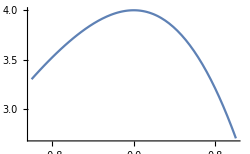

```mathematica
Plot[s[x],{x,-1,1},PlotRange->Automatic,ImageSize->250]
```

The answers in the green cells above match the answers in the text.

19.  (x-2)y'=x y, y[0]=4, x_1=2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=y[x_]=Sum[Subscript[a, m] x^m,{m,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

```mathematica
e2=(x-2) y'[x]-x y[x]==0
```

(-2+x) (a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5)-x (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5)==0

```mathematica
e3=Expand[e2]
```

-x a_0-2 a_1+x a_1-x^2 a_1-4 x a_2+2 x^2 a_2-x^3 a_2-6 x^2 a_3+3 x^3 a_3-x^4 a_3-8 x^3 a_4+4 x^4 a_4-x^5 a_4-10 x^4 a_5+5 x^5 a_5-x^6 a_5==0

```mathematica
e4=Collect[e3,x]
```

-2 a_1+x (-a_0+a_1-4 a_2)+x^2 (-a_1+2 a_2-6 a_3)+x^3 (-a_2+3 a_3-8 a_4)+x^4 (-a_3+4 a_4-10 a_5)-x^6 a_5+x^5 (-a_4+5 a_5)==0

Below: a_1 , which will be the coefficient of x in the final equation, has no business sticking out by itself.

```mathematica
e5=Solve[-2 Subscript[a, 1]==0,Subscript[a, 1]]
```

{{a_1→0}}

Below: This value of a_0 was set with the belief that it is necessary for the initial condition, y(0)=4.

```mathematica
e6=Solve[-Subscript[a, 0]+Subscript[a, 1]-4 Subscript[a, 2]==0,Subscript[a, 2]]/.{Subscript[a, 0]->4,Subscript[a, 1]->0}
```

{{a_2→-1}}

```mathematica
e7=Simplify[Solve[-Subscript[a, 1]+2 Subscript[a, 2]-6 Subscript[a, 3]==0,Subscript[a, 3]]/.{Subscript[a, 2]->-1,Subscript[a, 1]->0}]
```

{{a_3→-1/3}}

```mathematica
e8=Simplify[Solve[-Subscript[a, 2]+3 Subscript[a, 3]-8 Subscript[a, 4]==0,Subscript[a, 4]]/.{Subscript[a, 2]->-1,Subscript[a, 3]->-1/3}]
```

{{a_4→0}}

```mathematica
e9=Simplify[Solve[-Subscript[a, 3]+4 Subscript[a, 4]-10 Subscript[a, 5]==0,Subscript[a, 5]]/.{Subscript[a, 3]->-1/3,Subscript[a, 4]->0}]
```

{{a_5→1/30}}

Above: Discovery of a_5 gives all the coefficients necessary to express s up to fifth power of x.

```mathematica
e10=y[x]/.{Subscript[a, 0]->4,Subscript[a, 1]->0,Subscript[a, 2]->-1,Subscript[a, 3]->-1/3,Subscript[a, 4]->0,Subscript[a, 5]->1/30}
```

4-x^2-x^3/3+x^5/30

```mathematica
e11=s[x_]=e10
```

4-x^2-x^3/3+x^5/30

```mathematica
s[0]
```

4

```mathematica
s[2]
```

-8/5

```mathematica
Plot[s[x],{x,-1,1},PlotRange->Automatic,ImageSize->250]
```

-Graphics-